# 共形变换在求解本征值问题中的应用

```mathematica
Needs["NDSolve`FEM`"]
```

## 首先，确定题目所给式子对应的变换

```mathematica
w=(z+0.2z^2+0.2Exp[I d]z^3)/Sqrt[1+2*0.2^2+3*0.2^2]*R/.{R->1,d->Pi/3}
```

0.912871 (z+0.2 z^2+(0.1+0.173205 ⅈ) z^3)

```mathematica
initialregion=w/.{z->x+I y,R->1}//ComplexExpand
```

0.912871 x+0.182574 x^2+0.0912871 x^3-0.474342 x^2 y-0.182574 y^2-0.273861 x y^2+0.158114 y^3+ⅈ (0.158114 x^3+0.912871 y+0.365148 x y+0.273861 x^2 y-0.474342 x y^2-0.0912871 y^3)

```mathematica
first=(Refine[Re[initialregion],{x,y}∈ Reals]//Evaluate)
```

0.912871 x+0.182574 x^2+0.0912871 x^3-0.474342 x^2 y-0.182574 y^2-0.273861 x y^2+0.158114 y^3

```mathematica
second=Refine[Im[initialregion],{x,y}∈ Reals]//Evaluate
```

0.158114 x^3+0.912871 y+0.365148 x y+0.273861 x^2 y-0.474342 x y^2-0.0912871 y^3

## trans就是对圆盘进行形变的变换函数

```mathematica
trans=Function[{x,y},Evaluate[{first,second}]]
```

Function[{x,y},{0.912871 x+0.182574 x^2+0.0912871 x^3-0.474342 x^2 y-0.182574 y^2-0.273861 x y^2+0.158114 y^3,0.158114 x^3+0.912871 y+0.365148 x y+0.273861 x^2 y-0.474342 x y^2-0.0912871 y^3}]

## 在Mathematica中对它进行形变

```mathematica
region2=TransformedRegion[ImplicitRegion[x^2+y^2≤1,{x,y}],trans]
```

ParametricRegion[{{0.912871 x+0.182574 x^2+0.0912871 x^3-0.474342 x^2 y-0.182574 y^2-0.273861 x y^2+0.158114 y^3,0.158114 x^3+0.912871 y+0.365148 x y+0.273861 x^2 y-0.474342 x y^2-0.0912871 y^3},x^2+y^2≤1},{x,y}]

## 我们来看一下求出的区域

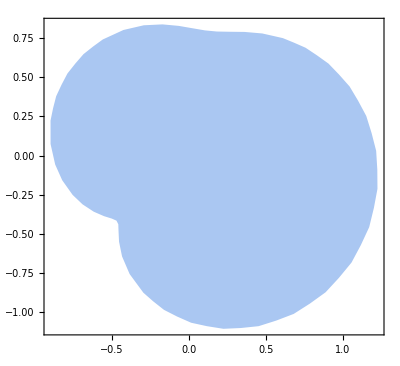

```mathematica
Region[region2,Axes->True,Frame->True]
```

## 接下来对该区域求本征值，由于系数当做1，所以实际上就是在求拉普拉斯算子的本征值

在求解前1000个本征值之前，我们先要对区域进行离散化。原因是如果在MMA中直接硬求本征值和本征函数的话，会消耗大量内存，没算完就已经因为内存溢出退出内核了。对区域进行离散化就是为了降低网格密度。

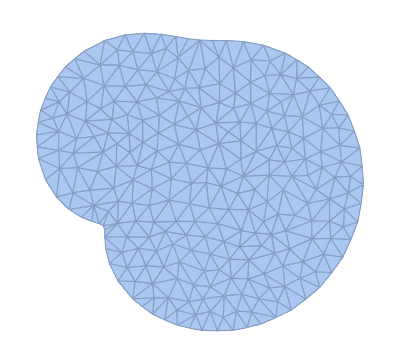

```mathematica
region3=DiscretizeRegion[region2,AccuracyGoal->13,PrecisionGoal->13]
```

```mathematica
{vals,funs}=NDEigensystem[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈region3,1000]//Quiet;
```

将前6个画出

```mathematica
Table[Plot3D[funs⟦i⟧,{x,y}∈region2,PlotRange->All,PlotLabel->vals⟦i⟧,PlotTheme->"Minimal",PerformanceGoal->"Speed"],{i,1,6}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
vals
```

# 用共形变换处理

```mathematica
ortho[l_,q_]:=Sqrt[2Pi NIntegrate[ρ BesselJ[l,BesselJZero[l,q]*ρ]^2,{ρ,0,1}]]
```

```mathematica
ortho[1000,1]//Timing
```

```mathematica
anaortho[l_,q_]:=ConditionalExpression[√π √(BesselJ[l,BesselJZero[l,q]]^2+BesselJ[1+l,BesselJZero[l,q]]^2-(2 l BesselJ[l,BesselJZero[l,q]] BesselJ[1+l,BesselJZero[l,q]])/BesselJZero[l,q]), l≥0&&BesselJZero[l,q]≥0]
```

```mathematica
GuessOrtho[l_,q_]:=√π √(BesselJ[l,BesselJZero[l,q]]^2+BesselJ[1+l,BesselJZero[l,q]]^2-(2 l BesselJ[l,BesselJZero[l,q]] BesselJ[1+l,BesselJZero[l,q]])/BesselJZero[l,q])
```

```mathematica
Basis[l_,q_][ρ_,ϕ_]:= GuessOrtho[l,q]*Exp[I l ϕ]*BesselJ[l,BesselJZero[l,q]*ρ]
```

```mathematica
T[ρ_,ϕ_]=Abs[D[w,z]/.{z->(x+I y)}/.{x->ρ Cos[ϕ],y->ρ Sin[ϕ]}]^2
```

0.833333 Abs[1+0.4 (ρ Cos[ϕ]+ⅈ ρ Sin[ϕ])+(0.3+0.519615 ⅈ) (ρ Cos[ϕ]+ⅈ ρ Sin[ϕ])^2]^2

```mathematica
M[l_,q_,ll_,qq_]:=
Module[{a=GuessOrtho[l,q]//N,b=GuessOrtho[ll,qq]//N,c=BesselJ[l,q]//N,d=BesselJ[ll,qq]//N,e=BesselJZero[l,q]//N,f=BesselJZero[ll,qq]//N},
{values,values1}={{},{}};
a*b/(e*f)*
NIntegrate[Exp[I (ll-l) ϕ]*ρ T[ρ,ϕ]*BesselJ[l,e*ρ]*BesselJ[ll,f*ρ],{ϕ,0,2Pi},{ρ,0,1},AccuracyGoal->2,PrecisionGoal->2]]
```

```mathematica
c=1;
```

```mathematica
tab=Monitor[Table[c++;M[x,y,z,j],{x,1,5},{y,1,5},{z,1,5},{j,1,5}],ProgressIndicator[c,{1,625}]];
```

```mathematica
(Map[{Opacity[#[[1]]],Hue[#[[1]]*100],Cuboid[#[[2]]]}&,MapIndexed[{#1,#2}&,tab[[1]],{-1}],{-3}]//Flatten//Partition[#,3]&)[[1;;125]]//Graphics3D
```

```mathematica
Table[tab[[i,i,i,i]],{i,1,5}]
```

{0.0161978,0.000709591,0.000124425,0.0000378791,0.0000147505}